```mathematica
LaunchKernels[]
```

```mathematica
Diff=1;
β=0;
θ=0;
α=0;
xzero=0.01;
sigma=0.001;

hx=0.001;
ht=0.01;

length = Floor[2/hx];
time =Floor[3/ht];
xi= Array[(#-length/2 -1)*hx&,{length+1}];
ti= Array[(#-1)*ht&,{time+1}];

ProbM=ConstantArray[0,{length+1, time+1}];
St=ConstantArray[0,{time}];
```

```mathematica
sol=NDSolve[{D[P[x,t],t]==Diff*D[(1+α*x^2)*(D[P[x,t],x]+β*(x+θ*x^3)*P[x,t])
,x] ,
P[-10,t]==0,
P[10,t]==0,
P[x,0]==1/(√π*sigma)Exp[(-(x-xzero)^2)/sigma^2]},
P,{x,-10,10},{t,0,10},AccuracyGoal->10];

Prob[x_,t_]:=P[x,t]/.sol;

For[j=1,j<length+1,j++,
For[s=1,s<time+1,s++,

ProbM[[j,s]]=Norm[Prob[xi[[j]],ti[[s]]]]; 
]
];



Export["C:\\Users\\Ritam\\Documents\\Wolfram Mathematica\\Electron Transfer\\PT_Theta_"<>ToString[θ]<>"_SolvationPhase_Alpha_"<>ToString[α]<>"_Beta_"<>ToString[β]<>"_x"<>ToString[xzero]<>".mat",ProbM];



For[s=1,s<time+1,s++,
St[[s]]=hx*Sum[xi[[j]]ProbM[[j,s]],{j,length+1}]; 
];



Export["C:\\Users\\Ritam\\Documents\\Wolfram Mathematica\\Electron Transfer\\ST_Theta_"<>ToString[θ]<>"_SolvationPhase_Alpha_"<>ToString[α]<>"_Beta_"<>ToString[β]<>"_x"<>ToString[xzero]<>".csv",St];
```

```mathematica
A=Export["C:\\Users\\Ritam\\Documents\\Wolfram Mathematica\\Electron Transfer\\ST_Theta_"<>ToString[θ]<>"_SolvationPhase_Alpha_"<>ToString[α]<>"_Beta_"<>ToString[β]<>"_x"<>ToString[xzero]<>".csv",St];
```

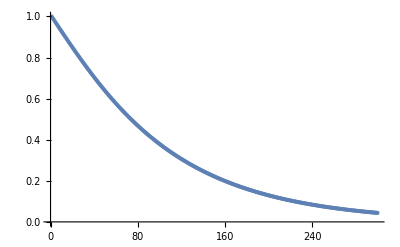

```mathematica
ListPlot[St/0.01]
```

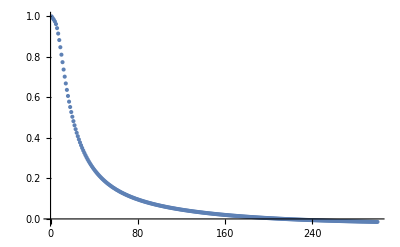

```mathematica
ListPlot[St/0.01, PlotRange->All]
```

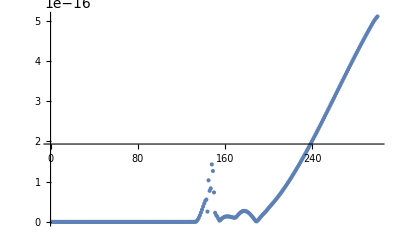

```mathematica
ListPlot[St/0.01, PlotRange->All]
```

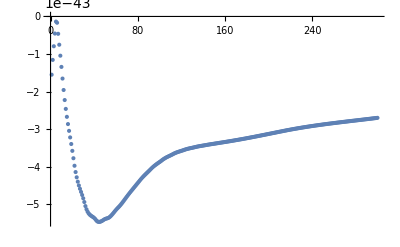

```mathematica
ListPlot[St/0.01, PlotRange->All]
```